```mathematica
raw = ImportString[" chirp0_0.1Dcsr.json, 2.383748254493385e-05, 0.0002634650988007763, 0.0002806055913115039
 chirp0_005.1Dcsr.json, 2.6097515769549958e-05, 0.00019601815051305602, 0.0001939935011409852
 chirp0_01.1Dcsr.json, 2.8396146687204098e-05, 0.00015928194033150214, 0.00015315054984232023
 chirp0_015.1Dcsr.json, 3.072566838616945e-05, 0.00013658293648854202, 0.00013236638650048532
 chirp0_02.1Dcsr.json, 3.3079781026537226e-05, 0.00012112958305934318, 0.00012085203991108827
 chirp0_05.1Dcsr.json, 4.751480495693093e-05, 7.970001537963314e-05, 0.00010188794158000298
 chirp0_0.2Dcsr.json, 2.4375605741747868e-05, 0.0003360137709624563, 0.0003245530302676438
 chirp0_005.2Dcsr.json, 2.6537972562744715e-05, 0.00024908835824689635, 0.00022737528729237024
 chirp0_01.2Dcsr.json, 2.8769580772848472e-05, 0.0002016094394410521, 0.00017900105478531092
 chirp0_015.2Dcsr.json, 3.105086607297616e-05, 0.00017093692757511465, 0.00015151694856240286
 chirp0_02.2Dcsr.json, 3.336479882638767e-05, 0.00014934981427679831, 0.00013492323619758377
 chirp0_05.2Dcsr.json, 4.766892500274214e-05, 8.93571768331806e-05, 0.00010472318083739066"]
```

{{ chirp0_0.1Dcsr.json,0.0000238375,0.000263465,0.000280606},{ chirp0_005.1Dcsr.json,0.0000260975,0.000196018,0.000193994},{ chirp0_01.1Dcsr.json,0.0000283961,0.000159282,0.000153151},{ chirp0_015.1Dcsr.json,0.0000307257,0.000136583,0.000132366},{ chirp0_02.1Dcsr.json,0.0000330798,0.00012113,0.000120852},{ chirp0_05.1Dcsr.json,0.0000475148,0.0000797,0.000101888},{ chirp0_0.2Dcsr.json,0.0000243756,0.000336014,0.000324553},{ chirp0_005.2Dcsr.json,0.000026538,0.000249088,0.000227375},{ chirp0_01.2Dcsr.json,0.0000287696,0.000201609,0.000179001},{ chirp0_015.2Dcsr.json,0.0000310509,0.000170937,0.000151517},{ chirp0_02.2Dcsr.json,0.0000333648,0.00014935,0.000134923},{ chirp0_05.2Dcsr.json,0.0000476689,0.0000893572,0.000104723}}

```mathematica
data1D = {
{" chirp0_0.1Dcsr.json",0,0.00002383748254493385,0.0002634650988007763,0.0002806055913115039},{" chirp0_005.1Dcsr.json",0.005,0.000026097515769549958,0.00019601815051305602,0.0001939935011409852},{" chirp0_01.1Dcsr.json",0.01,0.000028396146687204098,0.00015928194033150214,0.00015315054984232023},{" chirp0_015.1Dcsr.json",0.015,0.00003072566838616945,0.00013658293648854202,0.00013236638650048532},{" chirp0_02.1Dcsr.json",0.02,0.000033079781026537226,0.00012112958305934318,0.00012085203991108827},{" chirp0_05.1Dcsr.json",0.05,0.00004751480495693093,0.00007970001537963314,0.00010188794158000298}
};

data2D = {
{" chirp0_0.2Dcsr.json",0,0.000024375605741747868,0.0003360137709624563,0.0003245530302676438},{" chirp0_005.2Dcsr.json",0.005,0.000026537972562744715,0.00024908835824689635,0.00022737528729237024},{" chirp0_01.2Dcsr.json",0.01,0.000028769580772848472,0.0002016094394410521,0.00017900105478531092},{" chirp0_015.2Dcsr.json",0.015,0.00003105086607297616,0.00017093692757511465,0.00015151694856240286},{" chirp0_02.2Dcsr.json",0.02,0.00003336479882638767,0.00014934981427679831,0.00013492323619758377},{" chirp0_05.2Dcsr.json",0.05,0.00004766892500274214,0.0000893571768331806,0.00010472318083739066}
};
```

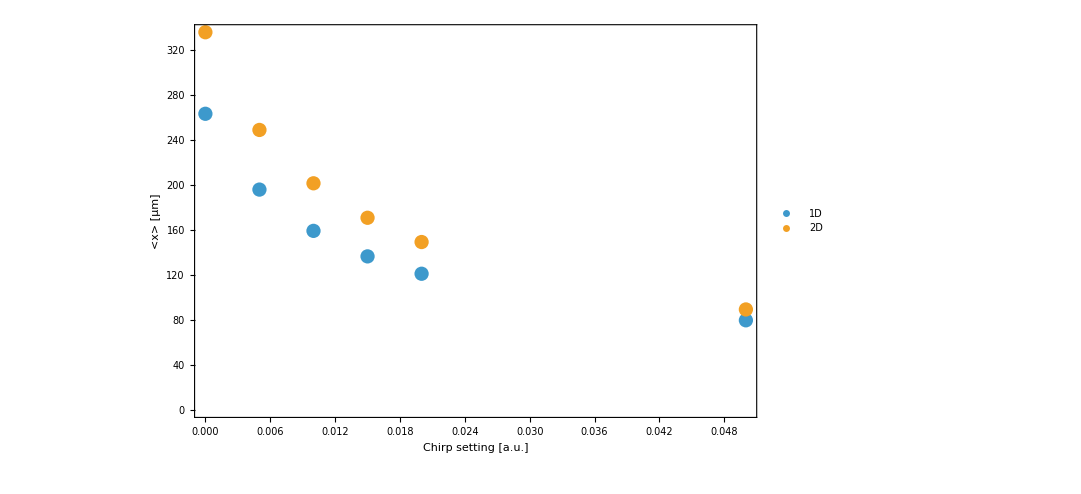

```mathematica
ListPlot[
{
{#[[1]],10^6*#[[2]]}&/@data1D[[All,{2,4}]],
{#[[1]],10^6*#[[2]]}&/@data2D[[All,{2,4}]]
},
ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"Chirp setting [a.u.]", "<x> [μm]"},
PlotLegends->Placed[{"1D","2D"},{0.9,0.85}]
]
```

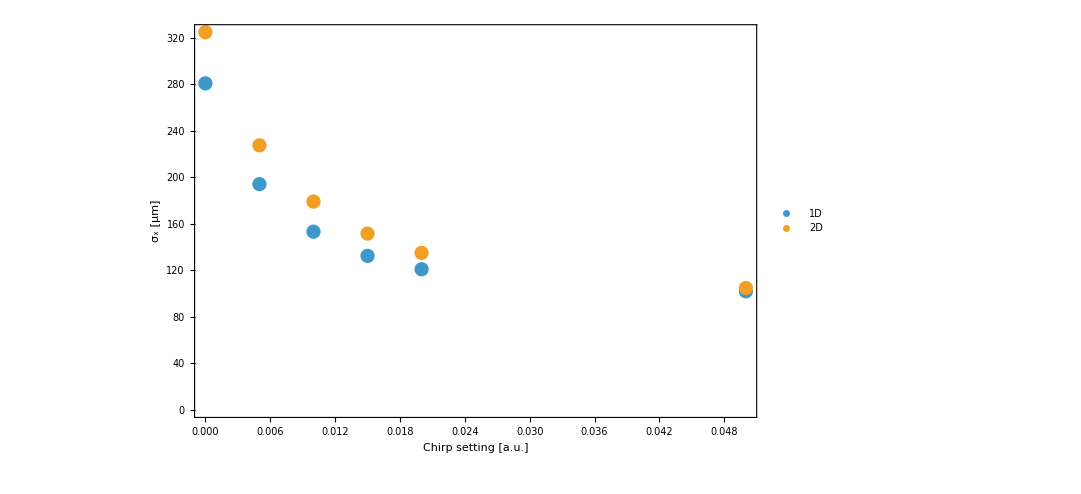

```mathematica
ListPlot[
{
{#[[1]],10^6*#[[2]]}&/@data1D[[All,{2,5}]],
{#[[1]],10^6*#[[2]]}&/@data2D[[All,{2,5}]]
},
ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"Chirp setting [a.u.]", "σ_x [μm]"},
PlotLegends->Placed[{"1D","2D"},{0.9,0.85}]
]
```